## Gaussian beam propagation

P.Huft

## Setup

import functions for Gaussian beams, propagation, etc.

```mathematica
SetDirectory[NotebookDirectory[]];
<<"optics.m"
```

Gaussian beam parameters:

## Propagate and plot the beam

### Waist transformation relation

check the relation w1w2 = λf/π, where w1,w2 are the full waists in the front and back focal plane of a lens with focal length f.

```mathematica
λ = 4.8*^-7;
inputWaist = {3.5*^-5,5*^-5}; (*system input waists wx,wy*)
colors = {Red,Green}; (*colors of waist plot lines*)
legends=Table[StringForm["``mm",waist/10^-3],{waist,inputWaist}];
f1 = .008; (*[m] lens focal length*)
lenses = {(*the system of optics*)
{IdentityMatrix[2],f1},
{MLens[f1],f1}};
```

```mathematica
waistfuncs ={};
For[i=1,i<Length[inputWaist]+1,i++,
q0 = -ⅈ π inputWaist[[i]]^2/λ;
AppendTo[waistfuncs,beamPropagate[q0,lenses,λ]](*system input beam*)
]
```

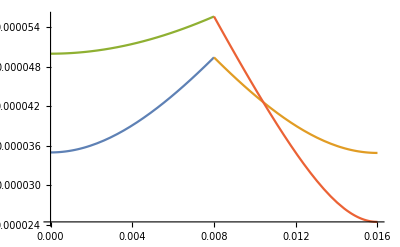

```mathematica
Plot[Evaluate[waistfuncs],{x,0,f1+f1},PlotRange->All]
```

```mathematica
(waistfuncs[[1,1]]/.x->10^-10)(waistfuncs[[1,2]]/.x->2f1)-(λ f1)/π
```

0.

```mathematica
(waistfuncs[[2,1]]/.x->10^-10)(waistfuncs[[2,2]]/.x->2f1)-(λ f1)/π
```

-2.06795×10^-25

### focal shift

The Gaussian back focal plane is always nearer to the lens than predicted by geometrical optics by an amount δ = |R(-z)| - z where z is the distance from the lens to the actual focal plane. This especially pronounced if the lens is in the near-field of the input beam, i.e. within the Rayleigh range (or equivalently, 2π Fresnel number < 1). This will always be true when focusing a well-collimated Gaussian beam.

```mathematica
Clear[w,R,z,zR]
```

```mathematica
R = z + zR^2/z; 
w =w0 √(1+z^2/zR^2);
zR = (π w0^2)/λ;
w^2/(λ R)//FullSimplify (*Fresnel number N(z) for a Gaussian beam. πN < 1 means we are within the Rayleigh range of the beam.*)
```

(z λ)/(π^2 w0^2)

Focal shift plots

Fresnel number, N(z=10mm)

10780.6

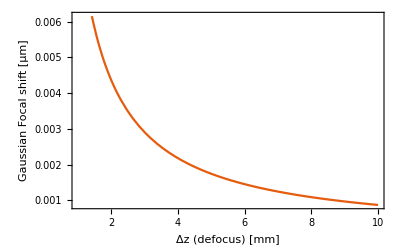

```mathematica
w0 = 1; (*μm*)
λ = 1.064;
"Fresnel number, N(z=10mm)"
(z λ)/(π^2 w0^2)/.z-> 10^5
Plot[(R-z)/.z-> zmm*10^3,{zmm,1,10},FrameLabel->{"Δz (defocus) [mm]","Gaussian Focal shift [μm]"},PlotTheme->"Scientific"]
```

Fresnel number, N(z=10mm)

0.0107806

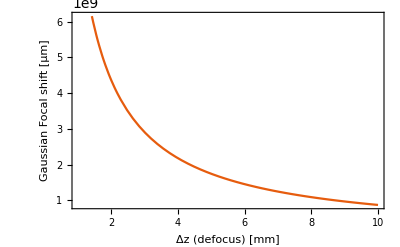

```mathematica
w0 = 1000; (*μm*)
λ = 1.064;
"Fresnel number, N(z=10mm)"
(z λ)/(π^2 w0^2)/.z-> 10^5
Plot[(R-z)/.z-> zmm*10^3,{zmm,1,10},FrameLabel->{"Δz (defocus) [mm]","Gaussian Focal shift [μm]"},PlotTheme->"Scientific"]
```